# Bulk Modulus

## structure factor

### load data

```mathematica
p0s={3.80,3.825,3.85};
 temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 recs=Table[Table[i,{i,0,9}],Length[p0s]];
 records=Table[Table[i,{i,10,19}],Length[p0s]];
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500,4500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
```

```mathematica
Length[recs[[1]]]
```

11

```mathematica
sks=Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/smallKSk_N4096_p","_T","_spacing","_idx","_rec",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,100000,tauEstimate[[p,T]]*100],records[[p,i]],recs[[p,rec]]},{3,4,8,0,0,0}],"Data"],{rec,Length[recs[[p]]]}],$Failed],{i,Length[records[[p]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec1.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec2.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
sksMean=Table[Table[Table[Mean[Flatten[Table[DeleteCases[Table[sks[[p,T,i,time,2,rec]],{i,Length[sks[[p,T]]]}],_Missing|_Part|0.],{time,Length[recs]}]]],{rec,Max[Table[Length[sks[[p,T,i,1,1]]],{i,Length[sks[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
sksMean[[1,2]]
```

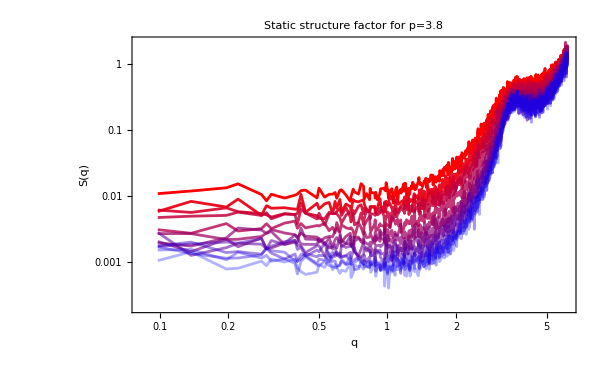
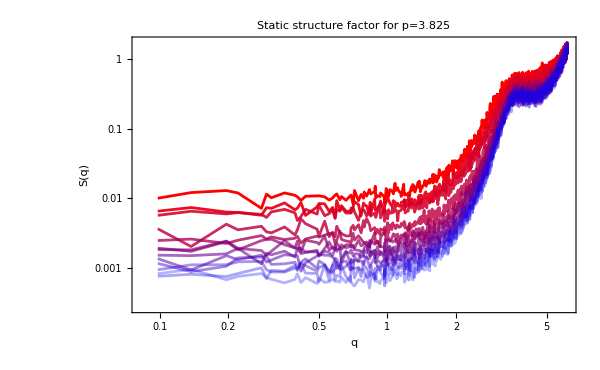
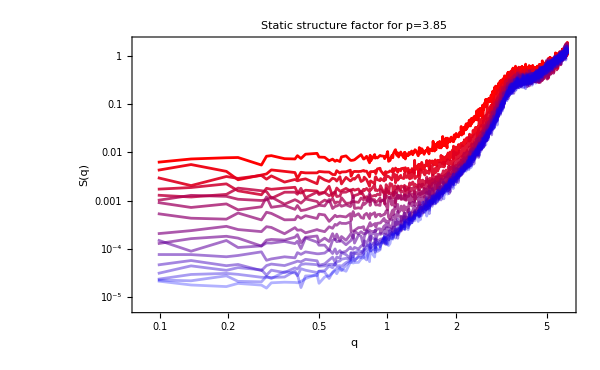

```mathematica
sqPLot=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean[[p,T,rec]]},{rec,Length[sksMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

```mathematica
compressibility=Table[Table[Mean[Table[sksMean[[p,T,rec]],{rec,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0111993,0.00684327,0.00561129,0.00504123,0.00344256,0.00260575,0.00240209,0.00199662,0.00191822,0.00190497,0.00144988,0.00133998,0.00118769,0.00101434},{0.0109739,0.00696973,0.00601992,0.00344702,0.00263291,0.00221314,0.00194449,0.0016015,0.00137607,0.00119588,0.00103276,0.000874898,0.000762296},{0.00745356,0.00385531,0.00281359,0.00174197,0.00142237,0.00106853,0.000803808,0.000473021,0.000250819,0.00015879,0.000129207,0.0000717807,0.0000478869,0.0000364499,0.0000279442,0.0000259797,0.0000188595}}

```mathematica
compressibility={{0.011199273784966107,0.006843271602432324,0.005611288719792794,0.005041234977461774,0.0034425583850431754,0.0026057510940828517,0.002402093767504809,0.0019966246441788602,0.0019182227717051852,0.0019049662456268918,0.001449880590064925,0.0013399825929035518,0.001187690840811528,0.001014343011690452},{0.010973863616378617,0.006969729232530318,0.006019921555357807,0.0034470215575048853,0.0026329094381145244,0.0022131356244573337,0.0019444910237750798,0.0016014985435969943,0.0013760687245457778,0.001195880727373862,0.0010327648584341675,0.000874898354553366,0.0007622957395221339},{0.007453560814727081,0.0038553113302460763,0.0028135912408168745,0.0017419724263324672,0.0014223701929428829,0.0010685323178511355,0.0008038075411382475,0.00047302076751918546,0.0002508192704905529,0.00015879046536729807,0.0001292071964184393,0.00007178071005006233,0.00004788692408399204,0.00003644992471026816,0.000027944243002211488,0.000025979680020164673,0.00001885945885242752}};
```

```mathematica
fitting=NonlinearModelFit[Table[{temperatures[[1,T]],1/(compressibility[[T]]/temperatures[[1,T]])},{T,Length[temperatures[[1]]]}],{A*x^B},{A,B},x]
```

FittedModel[14.5064 x^0.294567]

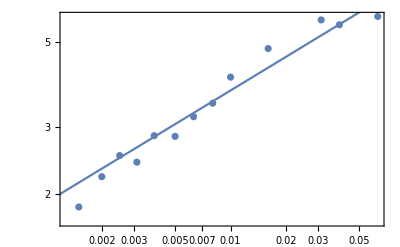

```mathematica
Show[ListLogLogPlot[Table[{temperatures[[1,T]],1/(compressibility[[T]]/temperatures[[1,T]])},{T,Length[temperatures[[1]]]}]],LogLogPlot[fitting[x],{x,0.000001,0.1}]]
```

## Numerical

### data loading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 records=Table[Table[i,{i,10,19}],Length[p0s]];
epsilons={{-0.001,0.,0.001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.825/isoCompression/timePressue_isoCompression_N4096_p3.8250_T0.00800000_epsilon0.00000000_idx10.nc"]
```

```mathematica
timePressure=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx12.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx15.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressure[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressureMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressure[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressure[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureMean
```

{{{{0.422435,0.433836,0.446251}},{{0.322941,0.333929,0.345035}},{{0.281129,0.291714,0.302406}},{{0.244687,0.254772,0.265014}},{{0.178785,0.187842,0.196946}},{{0.12188,0.129544,0.137061}},{{0.0990572,0.105768,0.112651}},{{0.0776427,0.0833365,0.0888063}},{{0.0593955,0.0642898,0.0682221}},{{0.0421304,0.0456132,0.0484917}},{{0.029454,0.0321637,0.0351424}},{{0.0240922,0.0270873,0.0302823}},{{0.0191463,0.0222616,0.0255752}},{{0.0145137,0.0174773,0.0214086}}},{{{0.368757,0.38051,0.391904}},{{0.275908,0.286473,0.297137}},{{0.237295,0.247382,0.25766}},{{0.145148,0.153837,0.162588}},{{0.0967217,0.104295,0.11187}},{{0.0781879,0.0851977,0.0922053}},{{0.0612173,0.0677694,0.0741582}},{{0.0474978,0.0534625,0.0593621}},{{0.0347663,0.0402149,0.0455359}},{{0.0262088,0.0313003,0.0362596}},{{0.0192835,0.0240272,0.028632}},{{0.0135299,0.0179894,0.0222536}},{{0.00785008,0.0119824,0.0158616}}},{{{0.231909,0.242287,0.252482}},{{0.114927,0.123061,0.13137}},{{0.0737175,0.0808885,0.0881134}},{{0.0340476,0.03994,0.0458253}},{{0.0242668,0.0298117,0.0353001}},{{0.0128329,0.0178257,0.0228266}},{{0.00873724,0.0134896,0.0182558}},{{0.00117457,0.00548879,0.00978234}},{{-0.00188092,0.00223054,0.00632159}},{{-0.00270104,0.00135252,0.00536283}},{{-0.00306612,0.000977688,0.00498945}},{{-0.00348997,0.000525444,0.00453321}},{{-0.00367279,0.000337077,0.00434656}},{{-0.00372655,0.000278862,0.00429957}},{{-0.00380967,0.000199681,0.00420753}},{{-0.00384064,0.000161359,0.0041756}},{{-0.00387737,0.000131308,0.00414086}}}}

```mathematica
pressurePlotS=Table[ListPlot[{Table[{timePressure[[1,T,1,1,1,1,i]],timePressure[[1,T,1,3,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}],Table[{timePressure[[1,T,1,3,1,1,i]],timePressure[[1,T,1,2,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}],Table[{timePressure[[1,T,1,3,1,1,i]],timePressure[[1,T,1,1,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}]},FrameLabel->{"t","P"},PlotStyle->redBluePlotConfig[3],PlotLabel->"T="<>ToString[temperatures[[1,T]]],Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

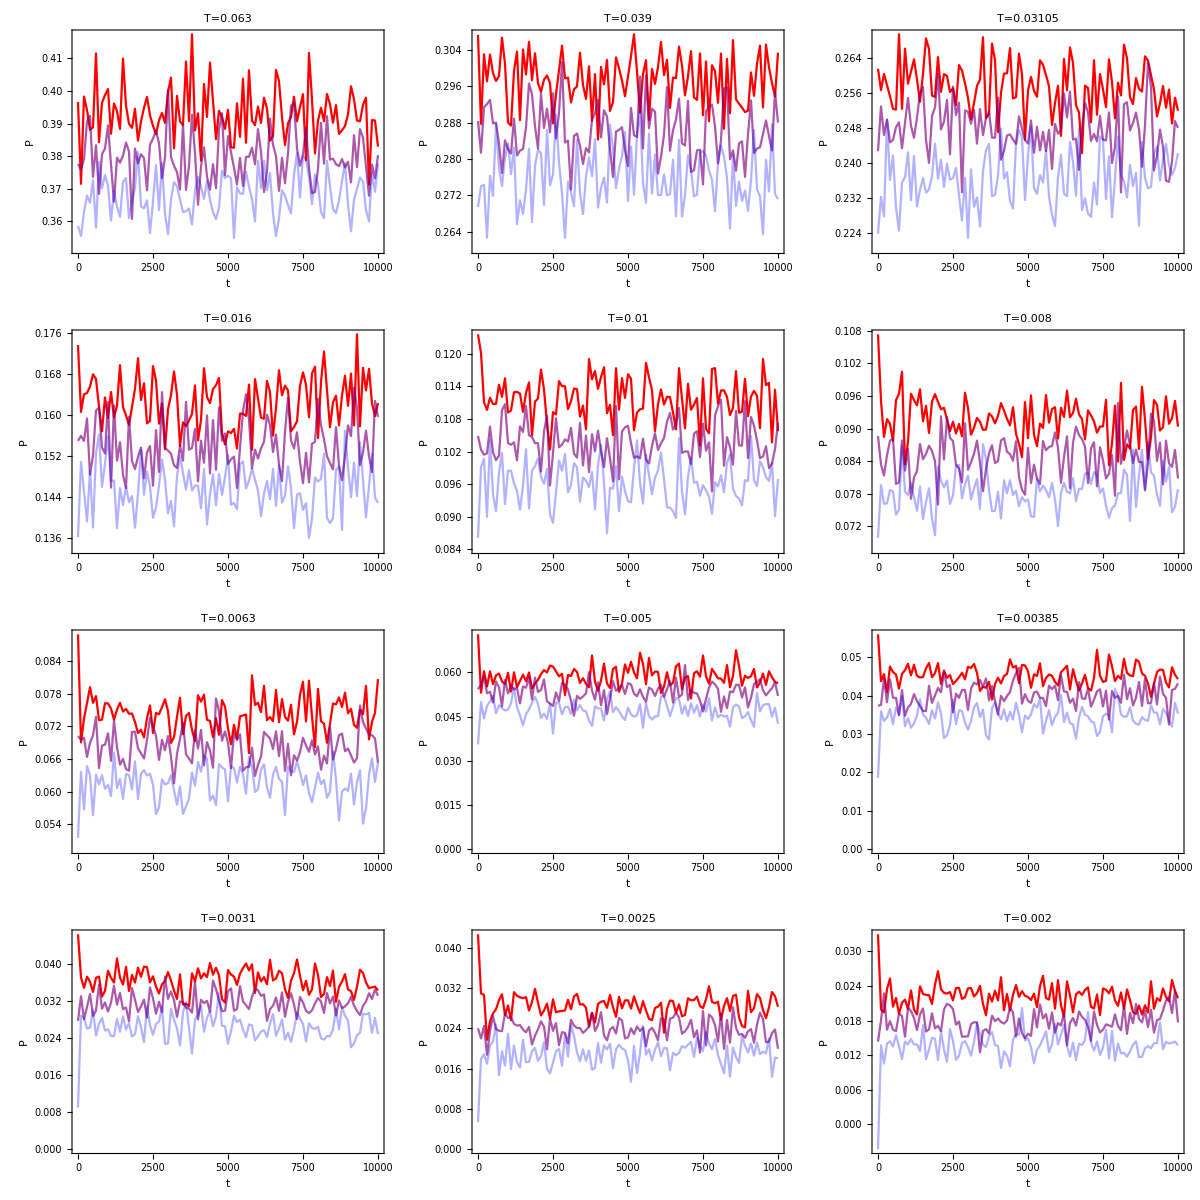

```mathematica
pressureTra=Grid[Partition[pressurePlotS,3]]
```

```mathematica
timePressureMean[[p,T,1,1]]
```

```mathematica
bulkModulus=Table[Table[(timePressureMean[[p,T,1,3]]-timePressureMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{5.95389,5.52358,5.31926,5.08188,4.54036,3.7952,3.39849,2.79091,2.20666,1.59032,1.42211,1.54752,1.60723,1.72373},{5.78675,5.30721,5.09104,4.3602,3.78716,3.50436,3.23523,2.96608,2.69242,2.5127,2.33714,2.18093,2.00287},{5.14308,4.11071,3.59895,2.94444,2.75832,2.49844,2.37965,2.15194,2.05063,2.01597,2.01389,2.00579,2.00484,2.00653,2.0043,2.00406,2.00456}}

```mathematica
bulkModulus=Table[-(Mean[Normal[timePressure[[1,T,1,1,1,2,100;;]]]]-Mean[Normal[timePressure[[1,T,1,3,1,2,100;;]]]])/2/0.001/2,{T,Length[temperatures[[1]]]}]
```

{5.76025,5.32531,5.07099,4.3956,3.82426,3.52433,3.2383,2.95894,2.66836,2.45754,2.29538,2.16032,2.02998}

```mathematica
fittingNumerical=NonlinearModelFit[Table[{temperatures[[1,T]],bulkModulus[[T]]},{T,Length[temperatures[[1]]]}],{A*x^B},{A,B},x]
```

FittedModel[13.1584 x^0.280852]

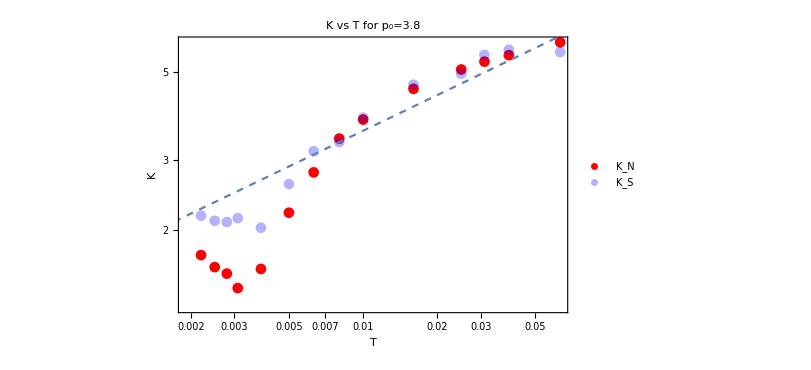
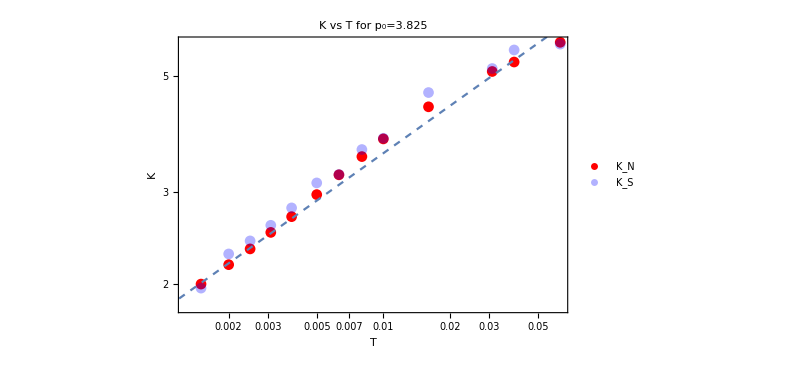
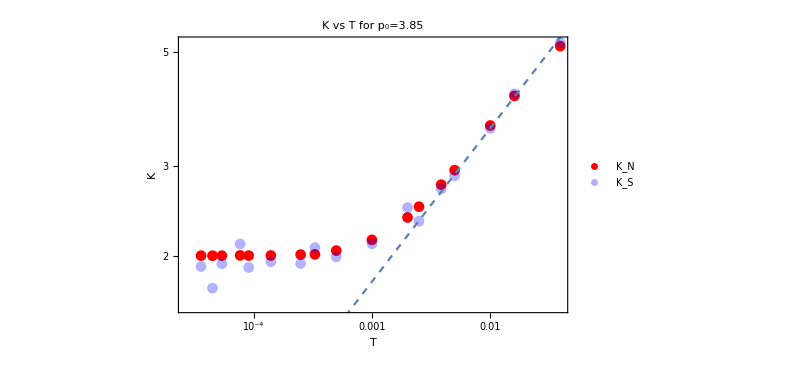

```mathematica
kPLots=Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],bulkModulus[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],1/(compressibility[[p,T]]/temperatures[[p,T]])},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[2],PlotLegends->{"K_N","K_S"}],LogLogPlot[14.158x^0.3,{x,0.000001,0.1},PlotStyle->Dashed]],{p,Length[p0s]}]
```

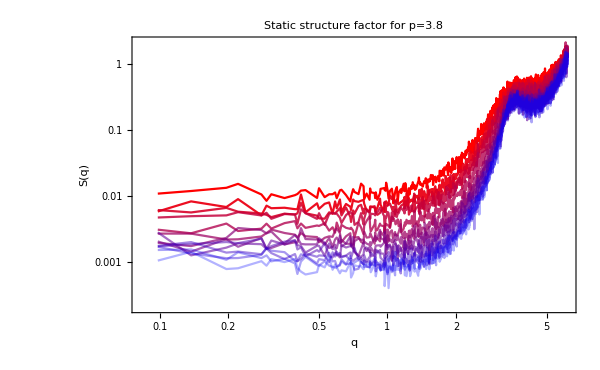
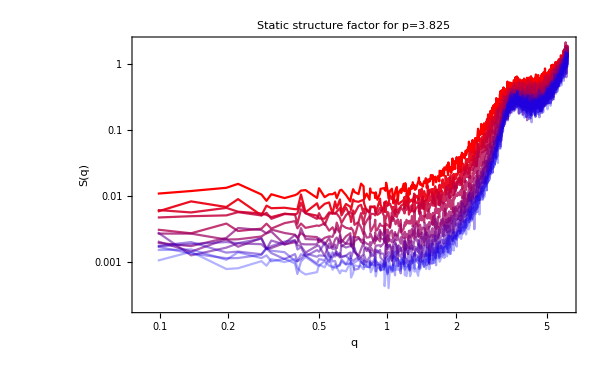
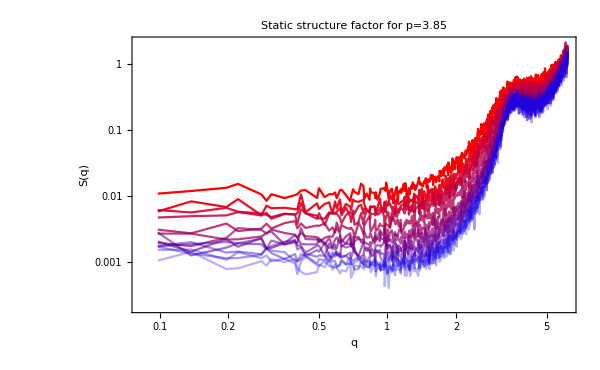
{-Graphics- | -Graphics-,-Graphics- | -Graphics-,-Graphics- | -Graphics-}

```mathematica
results=Table[Grid[Partition[{sqPLot[[p]],kPLots[[p]]},2]],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05162024/bulkModulus"<>ToString[p0s[[p]]]<>".jpeg",results[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05162024/bulkModulus3.8.jpeg,/home/chengling/Research/updates/05162024/bulkModulus3.825.jpeg,/home/chengling/Research/updates/05162024/bulkModulus3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05092024/kPLots.jpeg",kPLots,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/kPLots.jpeg

```mathematica
Export["/home/chengling/Research/updates/05092024/SqPlot.jpeg",sqPLot,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/SqPlot.jpeg

## larger ϵ

```mathematica
test=Import["/home/chengling/Downloads/timePressue_N4096_p3.8250_T0.06300000_epsilon0.05000000_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

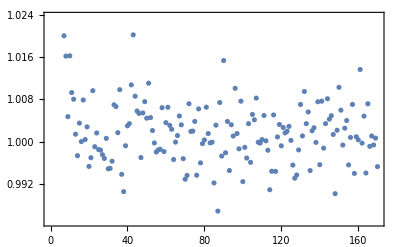

```mathematica
ListPlot[Table[{test[[1,i]],test[[2,i]]},{i,Length[test[[1]]]}]]
```

### smaller ϵ

### data loading

```mathematica
p0s={3.80}
```

{3.8}

```mathematica
temperatures={{00.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022}};
 records=Table[Table[i,{i,10,14}],Length[p0s]];
epsilons={{-0.001,0.,0.001},{-0.0001,0.,0.0001},{-0.00001,0.,0.00001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Normal[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_idx11.nc","Data"][[2,1;;10]]]
```

{0.0977089,0.0940092,0.0905322,0.0853599,0.086355,0.0931903,0.0997028,0.0911366,0.0882095,0.0934777}

```mathematica
Normal[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00010000_idx11.nc","Data"][[2,1;;10]]]
```

{0.0810542,0.0843894,0.0859837,0.0820457,0.0822349,0.0848988,0.0897095,0.0832979,0.0816164,0.0880473}

```mathematica
timePressureAreaLowT=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA1.0000_KP0.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon-0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00000000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_KA1.0000_KP0.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaLowT[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressurePeriLowT=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA0.0000_KP1.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon-0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00000000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_KA0.0000_KP1.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaLowTMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressureAreaLowT[[p,T,ep,epi,rec,2,100;;]]]],{rec,Length[timePressureAreaLowT[[p,T,ep,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureAreaLowTMean
```

{{{{-0.00144368,0.0025054,0.00645362},{0.00211018,0.0025054,0.00289917},{0.00246483,0.0025054,0.00254526}},{{-0.00189261,0.00205496,0.00599583},{0.00166165,0.00205496,0.00244889},{0.00201634,0.00205496,0.00209388}},{{-0.00230927,0.00163236,0.00556883},{0.00124006,0.00163236,0.0020234},{0.0015921,0.00163236,0.00167426}},{{-0.00259977,0.00133148,0.00527305},{0.000942395,0.00133148,0.00172747},{0.00129882,0.00133148,0.00137278}},{{-0.00272235,0.00121418,0.00516026},{0.000824262,0.00121418,0.00161268},{0.00118027,0.00121418,0.00125868}},{{-0.00284426,0.00110095,0.00505295},{0.000703312,0.00110095,0.00149482},{0.00106025,0.00110095,0.00113819}},{{-0.00296533,0.00097994,0.00494397},{0.000587997,0.00097994,0.00137741},{0.000943839,0.00097994,0.00102406}}}}

```mathematica
timePressurePeriLowTMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressurePeriLowT[[p,T,ep,epi,rec,2,100;;]]]],{rec,Length[timePressurePeriLowT[[p,T,ep,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressurePeriLowTMean
```

```mathematica
{{{{0.07906938699742307,0.08085538437184953,0.08233544172286074},{0.08065373142508657,0.08085538437184953,0.08085233060852243},{0.08075531147262649,0.08085538437184953,0.08083832870324859}},{{0.061288592995715596,0.062322804105488974,0.06242185480159304},{0.06232720382590027,0.062322804105488974,0.062355901889091236},{0.062353874072793795,0.062322804105488974,0.06236295557652198}},{{0.04423404996124854,0.04403304674631475,0.04329183966084848},{0.04415878351043161,0.04403304674631475,0.043797394971038565},{0.043959223494953625,0.04403304674631475,0.04420970389720612}},{{0.03199895473505895,0.03061029291610294,0.029892078180032103},{0.03102810544611785,0.03061029291610294,0.03062791830693571},{0.03111207759202674,0.03061029291610294,0.03064919586947573}},{{0.026804002196563193,0.025659193748644032,0.025166039180709494},{0.02607878755477542,0.025659193748644032,0.0259211497009582},{0.026146096111457046,0.025659193748644032,0.026039015898327494}},{{0.02194745782342335,0.021205154634139127,0.0209941357582334},{0.021117713410712755,0.021205154634139127,0.02115027332175218},{0.02119240375128361,0.021205154634139127,0.021074842405703585}},{{0.017326167035829593,0.016367823266489293,0.016804078656910318},{0.016715566446924526,0.016367823266489293,0.01647987263768877},{0.016663276686502283,0.016367823266489293,0.016743634363136296}}}}
```

{{{{0.0790694,0.0808554,0.0823354},{0.0806537,0.0808554,0.0808523},{0.0807553,0.0808554,0.0808383}},{{0.0612886,0.0623228,0.0624219},{0.0623272,0.0623228,0.0623559},{0.0623539,0.0623228,0.062363}},{{0.044234,0.044033,0.0432918},{0.0441588,0.044033,0.0437974},{0.0439592,0.044033,0.0442097}},{{0.031999,0.0306103,0.0298921},{0.0310281,0.0306103,0.0306279},{0.0311121,0.0306103,0.0306492}},{{0.026804,0.0256592,0.025166},{0.0260788,0.0256592,0.0259211},{0.0261461,0.0256592,0.026039}},{{0.0219475,0.0212052,0.0209941},{0.0211177,0.0212052,0.0211503},{0.0211924,0.0212052,0.0210748}},{{0.0173262,0.0163678,0.0168041},{0.0167156,0.0163678,0.0164799},{0.0166633,0.0163678,0.0167436}}}}

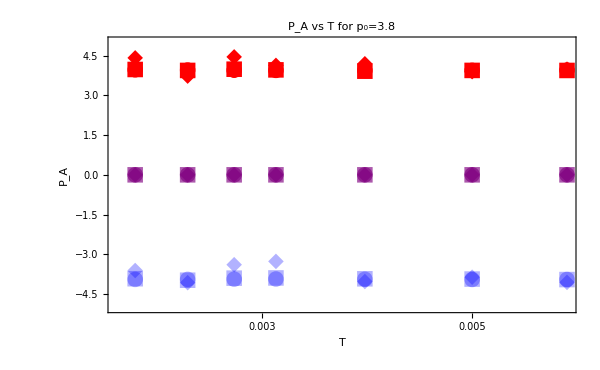

```mathematica
areaPressureLowTPlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,3]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,2]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,1]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_A"},ImageSize->600,PlotLabel->"P_A vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->{All,{-5,5}},PlotMarkers->{{"●",16},{"●",16},{"●",16}}],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,3]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,2]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,1]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotMarkers->{{"■",16},{"■",16},{"■",16}}],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,3]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,2]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,1]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotMarkers->{{"◆",16},{"◆",16},{"◆",16}}]],{p,Length[p0s]}];
Column[areaPressureLowTPlots]
```

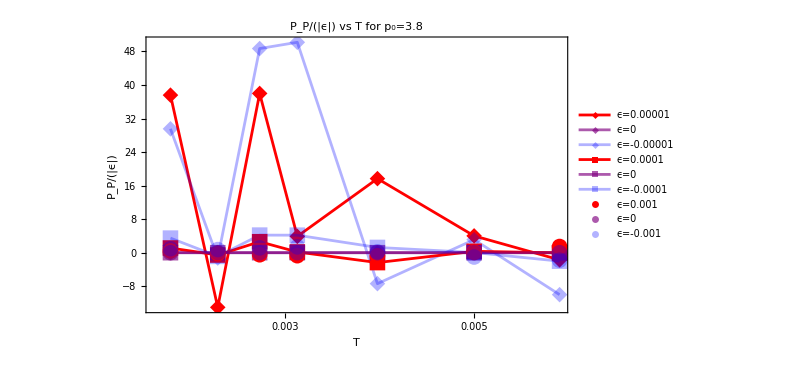

```mathematica
periPressureLowTPlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,3]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,2]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,1]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_P/(|ϵ|)"},ImageSize->600,PlotLabel->"P_P/(|ϵ|) vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.00001","ϵ=0","ϵ=-0.00001"},PlotMarkers->{{"◆",16},{"◆",16},{"◆",16}},Joined->True],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,3]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,2]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,1]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.0001","ϵ=0","ϵ=-0.0001"},PlotMarkers->{{"■",16},{"■",16},{"■",16}},Joined->True],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,3]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,2]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,1]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.001","ϵ=0","ϵ=-0.001"},PlotMarkers->{{"●",16},{"●",16},{"●",16}}]],{p,Length[p0s]}];
Column[periPressureLowTPlots]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/LowTPressue.jpeg",Grid[Partition[{areaPressureLowTPlots[[1]],periPressureLowTPlots[[1]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/LowTPressue.jpeg

## A, P contributions

### data loading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 records=Table[Table[i,{i,10,14}],Length[p0s]];
epsilons={{-0.001,0.,0.001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.825/isoCompression/timePressue_isoCompression_N4096_p3.8250_T0.00800000_epsilon0.00000000_KA1.0000_KP0.0000_idx11.nc"]
```

{/firstValue,/secondValue}

```mathematica
timePressureArea=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA1.0000_KP0.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA1.0000_KP0.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureArea[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressurePeri=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA0.0000_KP1.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA0.0000_KP1.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressureArea[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressureArea[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureAreaSTD=Table[Table[
Table[Table[StandardDeviation[Flatten[Table[Flatten[Normal[timePressureArea[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressureArea[[p,T,1,epi]]]}]]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{{0.000414411,0.000423263,0.00040856}},{{0.000270707,0.000273518,0.000270283}},{{0.000222901,0.000221877,0.000221376}},{{0.000185113,0.000184537,0.000182957}},{{0.000126263,0.00012656,0.000124394}},{{0.0000856455,0.0000847029,0.0000840701}},{{0.0000710583,0.0000700949,0.0000698729}},{{0.0000590076,0.0000578246,0.0000573789}},{{0.0000493138,0.0000484005,0.0000487899}},{{0.0000405465,0.0000405644,0.0000415107}},{{0.0000345773,0.0000338282,0.0000325722}},{{0.0000318755,0.0000311612,0.0000292934}},{{0.0000289705,0.0000285696,0.0000264052}},{{0.0000262592,0.0000242129,0.0000240029}}},{{{0.00058222,0.000419618,0.000421741}},{{0.00027945,0.000277065,0.000275457}},{{0.000230645,0.000228866,0.000227725}},{{0.000132996,0.000131857,0.000131532}},{{0.0000909413,0.0000905342,0.0000888408}},{{0.0000763019,0.0000758379,0.0000751874}},{{0.0000634091,0.0000628078,0.0000618937}},{{0.0000529283,0.0000527296,0.0000519477}},{{0.00004345,0.0000427996,0.00004229}},{{0.0000368997,0.0000365331,0.0000360113}},{{0.0000313771,0.0000309141,0.0000304575}},{{0.0000263867,0.0000260294,0.000025717}},{{0.0000213567,0.000020928,0.0000207888}}},{{{0.000287659,0.000286703,0.000284358}},{{0.000139807,0.00013827,0.00013672}},{{0.000096179,0.0000950784,0.000095058}},{{0.0000569646,0.0000562435,0.000055618}},{{0.0000468538,0.000046587,0.000045754}},{{0.0000340381,0.0000335483,0.0000332152}},{{0.000028617,0.0000284742,0.0000281555}},{{0.0000167324,0.0000164824,0.0000163601}},{{9.26199×10^-6,9.255×10^-6,9.18598×10^-6}},{{6.41668×10^-6,6.41482×10^-6,6.40703×10^-6}},{{5.01455×10^-6,5.03646×10^-6,5.00628×10^-6}},{{2.91564×10^-6,2.94024×10^-6,2.90596×10^-6}},{{1.93777×10^-6,1.93052×10^-6,1.93395×10^-6}},{{1.65063×10^-6,1.63204×10^-6,1.62944×10^-6}},{{1.17872×10^-6,1.16794×10^-6,1.154×10^-6}},{{9.8404×10^-7,9.72863×10^-7,9.73777×10^-7}},{{7.86386×10^-7,7.77363×10^-7,7.849×10^-7}}}}

```mathematica
timePressureAreaMean
```

{{{{0.0140905,0.0180315,0.0219718}},{{0.0080024,0.0119483,0.0158958}},{{0.00586672,0.00981674,0.0137672}},{{0.00419569,0.0081446,0.0120945}},{{0.00159747,0.00554998,0.0095068}},{{-0.000237873,0.0037165,0.00767001}},{{-0.000878947,0.00307181,0.00702349}},{{-0.00144368,0.0025054,0.00645362}},{{-0.00189261,0.00205496,0.00599583}},{{-0.00230927,0.00163236,0.00556883}},{{-0.00259977,0.00133148,0.00527305}},{{-0.00272235,0.00121418,0.00516026}},{{-0.00284426,0.00110095,0.00505295}},{{-0.00296533,0.00097994,0.00494397}}},{{{0.014429,0.0183947,0.0223345}},{{0.00834015,0.0122811,0.0162313}},{{0.00618756,0.0101336,0.0140804}},{{0.00187662,0.00583121,0.00978733}},{{0.0000246569,0.0039824,0.00794298}},{{-0.000624536,0.00333399,0.00729838}},{{-0.00119532,0.00276686,0.00673267}},{{-0.00165008,0.00231563,0.00628325}},{{-0.00207096,0.00189756,0.00586778}},{{-0.00236025,0.00161179,0.00558379}},{{-0.00260262,0.00137101,0.00534516}},{{-0.00281613,0.00115843,0.00513513}},{{-0.00304721,0.000931776,0.00491299}}},{{{0.00870436,0.0126411,0.0165781}},{{0.00217335,0.00612192,0.010076}},{{0.000276245,0.00423507,0.0081956}},{{-0.00146175,0.00250685,0.00648034}},{{-0.00190784,0.00206582,0.00604389}},{{-0.00247921,0.00150064,0.00548514}},{{-0.00271311,0.00127045,0.00525777}},{{-0.00324753,0.000744028,0.00473865}},{{-0.00357632,0.000419174,0.00441828}},{{-0.0037054,0.000291455,0.00429198}},{{-0.00377063,0.000226765,0.00422777}},{{-0.00386567,0.000132148,0.00413375}},{{-0.00391039,0.0000874222,0.00408936}},{{-0.00392342,0.0000744125,0.0040762}},{{-0.00394524,0.0000526859,0.00405456}},{{-0.00395383,0.0000440271,0.00404601}},{{-0.00396257,0.0000353738,0.00403728}}}}

```mathematica
timePressurePeriMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressurePeri[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressurePeri[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressurePeriSTD=Table[Table[
Table[Table[StandardDeviation[Flatten[Table[Flatten[Normal[timePressurePeri[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressurePeri[[p,T,1,epi]]]}]]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{{0.0073468,0.00752817,0.00720491}},{{0.00602867,0.00610968,0.00597358}},{{0.00553784,0.00551688,0.00544551}},{{0.0050925,0.00506519,0.0050596}},{{0.00430651,0.00430241,0.00426798}},{{0.00366786,0.00363661,0.00366352}},{{0.00338057,0.00339608,0.00337873}},{{0.00307437,0.00314316,0.0031433}},{{0.00289921,0.00286141,0.00303903}},{{0.00261702,0.00274443,0.00291333}},{{0.00243521,0.00241743,0.00241448}},{{0.00231618,0.00233986,0.00226139}},{{0.0022019,0.00221815,0.00210897}},{{0.00209316,0.00196374,0.00201977}}},{{{0.0100903,0.00753333,0.00754957}},{{0.00627427,0.00623018,0.00618455}},{{0.00579747,0.00568113,0.00563497}},{{0.00444909,0.00440589,0.00440038}},{{0.00369186,0.00367215,0.00366319}},{{0.00336414,0.00336423,0.00335741}},{{0.00303366,0.00304356,0.00305914}},{{0.00276292,0.00276523,0.00277839}},{{0.00248499,0.00248463,0.00250589}},{{0.00226496,0.00225726,0.00227066}},{{0.00205608,0.00207228,0.00207659}},{{0.00187741,0.0018772,0.00186739}},{{0.00162643,0.0016221,0.00163332}}},{{{0.00647911,0.00643182,0.00642638}},{{0.00458966,0.00455559,0.00453625}},{{0.00379566,0.00375662,0.00375457}},{{0.00281539,0.0028035,0.00280115}},{{0.00250688,0.00252309,0.00249634}},{{0.00205475,0.00204509,0.00204813}},{{0.00185588,0.00183895,0.00184706}},{{0.00132611,0.00132402,0.00133635}},{{0.000954141,0.00093958,0.000948292}},{{0.000774515,0.000772982,0.000775328}},{{0.000671266,0.000670814,0.000669139}},{{0.000503994,0.000501418,0.000502217}},{{0.000407335,0.000405406,0.000404785}},{{0.000374002,0.000373205,0.000374365}},{{0.000313671,0.000312688,0.000313517}},{{0.000286502,0.000286528,0.000283332}},{{0.000257366,0.000256479,0.000255947}}}}

```mathematica
timePressurePeriMean
```

{{{{0.408374,0.416186,0.424312}},{{0.314931,0.321953,0.329143}},{{0.275211,0.281912,0.288684}},{{0.240518,0.246634,0.252887}},{{0.177215,0.182322,0.187489}},{{0.12214,0.125925,0.129319}},{{0.0999876,0.102784,0.105471}},{{0.0790694,0.0808554,0.0823354}},{{0.0612886,0.0623228,0.0624219}},{{0.044234,0.044033,0.0432918}},{{0.031999,0.0306103,0.0298921}},{{0.026804,0.0256592,0.025166}},{{0.0219475,0.0212052,0.0209941}},{{0.0173262,0.0163678,0.0168041}}},{{{0.354087,0.36217,0.369782}},{{0.267651,0.274199,0.281031}},{{0.231075,0.237263,0.243512}},{{0.143256,0.14796,0.152833}},{{0.0967254,0.10032,0.103979}},{{0.0788124,0.0818662,0.0849615}},{{0.0624381,0.0649832,0.067463}},{{0.0490592,0.0511081,0.0530988}},{{0.0368705,0.0383402,0.0396621}},{{0.0285322,0.029657,0.0305898}},{{0.0219189,0.0227605,0.0231763}},{{0.0163812,0.0167821,0.0170285}},{{0.0108706,0.0110116,0.0111103}}},{{{0.223326,0.22959,0.235857}},{{0.11273,0.116922,0.121317}},{{0.0734375,0.0766399,0.0799393}},{{0.0355214,0.0374348,0.0393668}},{{0.02616,0.0277562,0.0292434}},{{0.0153255,0.0163246,0.0173089}},{{0.011454,0.0122097,0.0130124}},{{0.00443139,0.00475465,0.00502837}},{{0.00170007,0.00180452,0.00188154}},{{0.000992053,0.00104762,0.0010635}},{{0.000698839,0.000760108,0.000752303}},{{0.000369896,0.000386916,0.000398994}},{{0.000234301,0.000237081,0.000269536}},{{0.000186147,0.000205235,0.000214325}},{{0.000129685,0.000151084,0.000163199}},{{0.000107793,0.000118776,0.000145319}},{{0.0000830756,0.0000973155,0.000102743}}}}

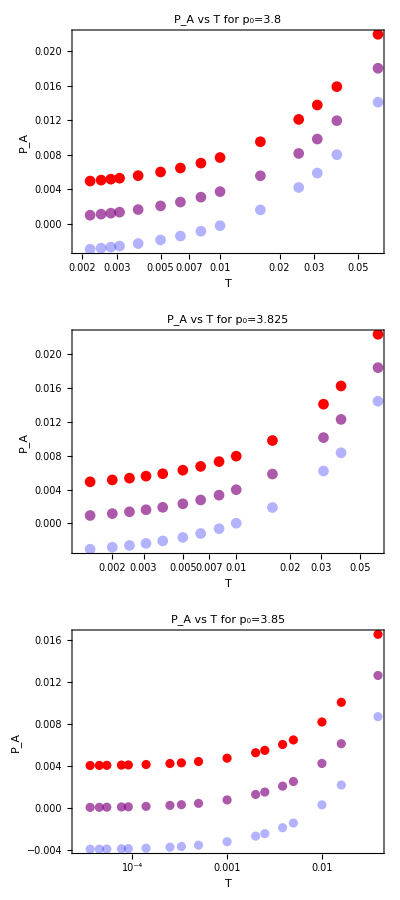

```mathematica
areaPressurePlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,1]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_A"},ImageSize->600,PlotLabel->"P_A vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All]],{p,Length[p0s]}];
Column[areaPressurePlots]
```

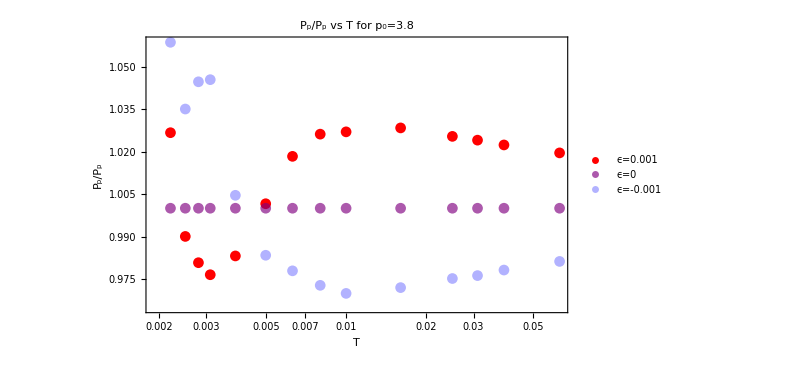
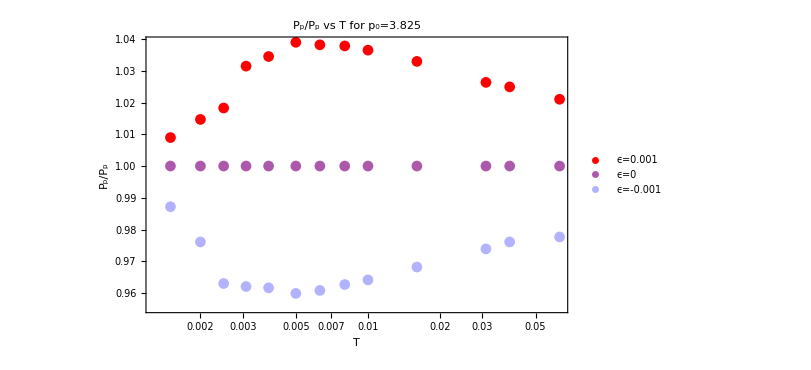
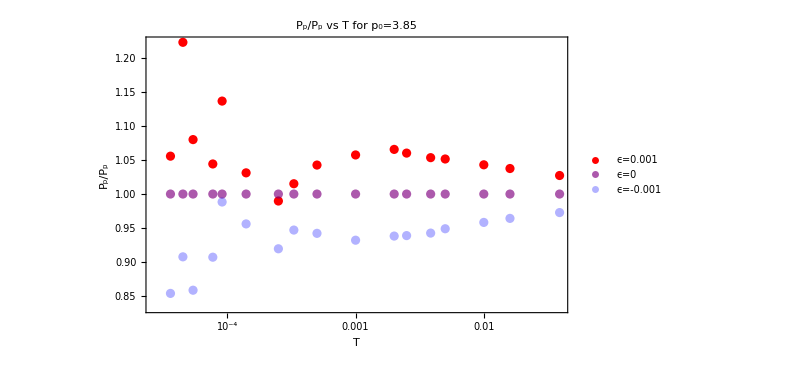

```mathematica
periPressurePlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,3]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,2]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,1]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_p/P_p"},ImageSize->600,PlotLabel->"P_p/P_p vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.001","ϵ=0","ϵ=-0.001"}]],{p,Length[p0s]}];
Column[periPressurePlots]
```

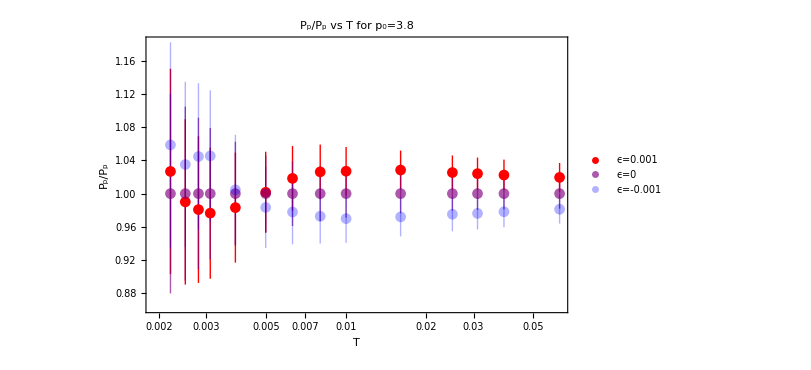
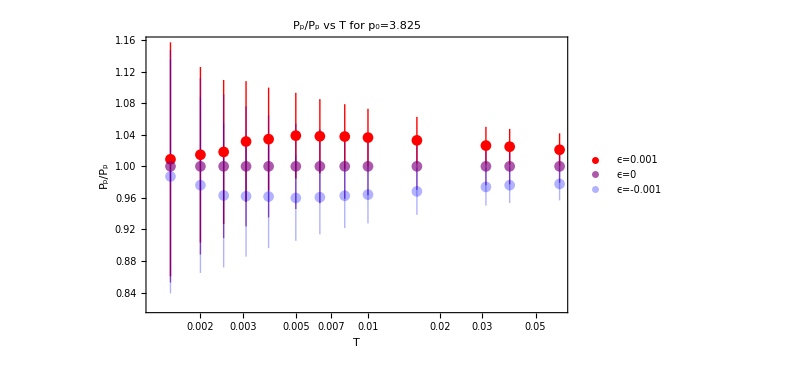
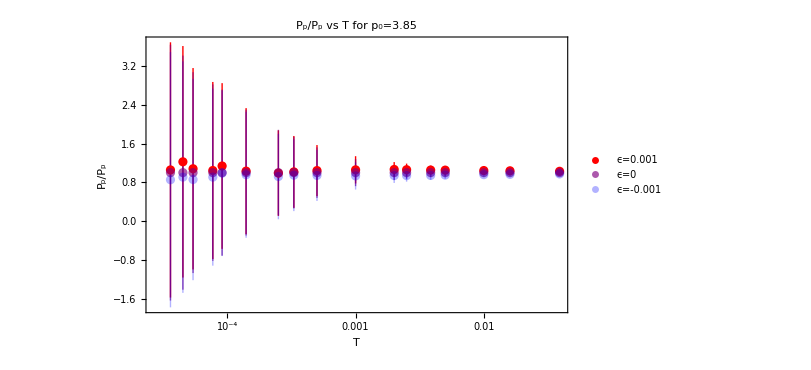

```mathematica
periPressurePlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],Around[timePressurePeriMean[[p,T,1,3]]/timePressurePeriMean[[p,T,1,2]],timePressurePeriSTD[[p,T,1,3]]/timePressurePeriMean[[p,T,1,2]]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],Around[timePressurePeriMean[[p,T,1,2]]/timePressurePeriMean[[p,T,1,2]],timePressurePeriSTD[[p,T,1,2]]/timePressurePeriMean[[p,T,1,2]]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],Around[timePressurePeriMean[[p,T,1,1]]/timePressurePeriMean[[p,T,1,2]],timePressurePeriSTD[[p,T,1,3]]/timePressurePeriMean[[p,T,1,2]]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_p/P_p"},ImageSize->600,PlotLabel->"P_p/P_p vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.001","ϵ=0","ϵ=-0.001"}]],{p,Length[p0s]}];
Column[periPressurePlots]
```

```mathematica
bulkModulusArea=Table[Table[(timePressureAreaMean[[p,T,1,3]]-timePressureAreaMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.97033,1.97335,1.97513,1.97469,1.97733,1.97697,1.97561,1.97433,1.97211,1.96953,1.9682,1.97065,1.9743,1.97733},{1.97637,1.9728,1.97322,1.97768,1.97958,1.98073,1.982,1.98333,1.98468,1.98601,1.98694,1.98781,1.99005},{1.96843,1.97566,1.97984,1.98552,1.98793,1.99109,1.99272,1.99655,1.99865,1.99934,1.9996,1.99986,1.99994,1.99991,1.99995,1.99996,1.99996}}

```mathematica
bulkModulusPeri=Table[Table[(timePressurePeriMean[[p,T,1,3]]-timePressurePeriMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{3.98455,3.55301,3.36809,3.09234,2.5685,1.79459,1.37081,0.816514,0.283315,-0.235553,-0.526719,-0.409491,-0.238331,-0.130522},{3.92357,3.34493,3.10909,2.39436,1.8135,1.53728,1.25623,1.00989,0.697894,0.514401,0.314362,0.161834,0.0599226},{3.13279,2.14667,1.62545,0.961345,0.77085,0.495848,0.389603,0.149245,0.0453676,0.0178629,0.013366,0.00727436,0.00880882,0.00704454,0.00837866,0.00938152,0.00491682}}

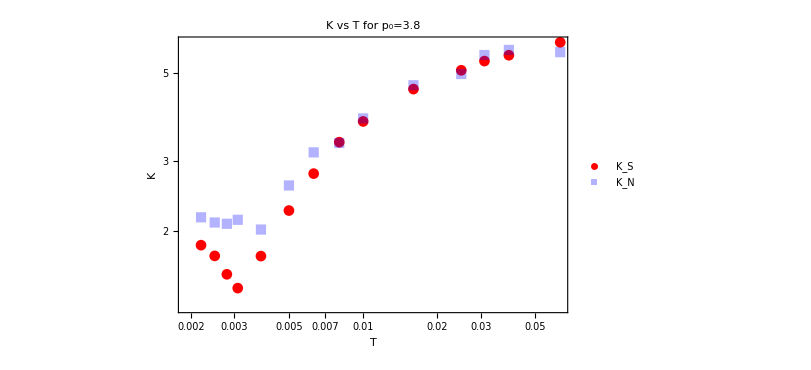
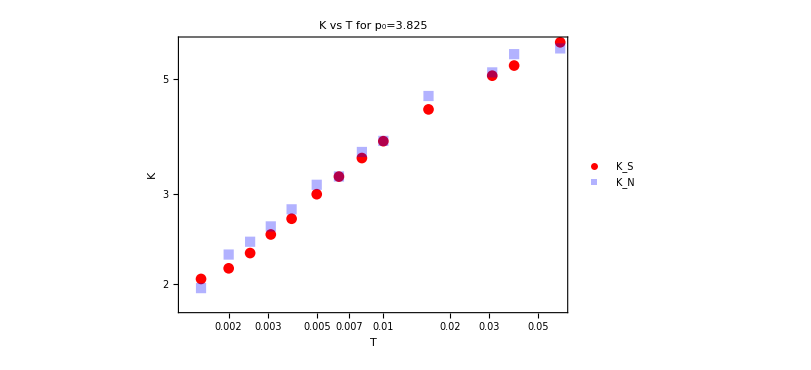
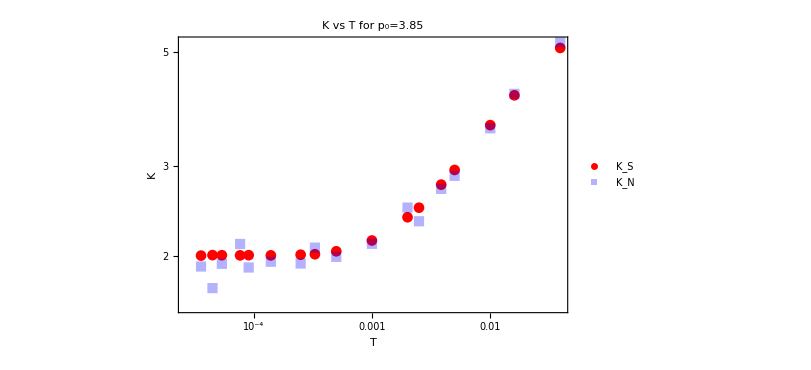

```mathematica
modulusPlot=Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]+bulkModulusArea[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],1/(compressibility[[p,T]]/temperatures[[p,T]])},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotMarkers->Automatic,PlotLegends->{"K_S","K_N"},PlotStyle->redBluePlotConfig[2]]],{p,Length[p0s]}]
```

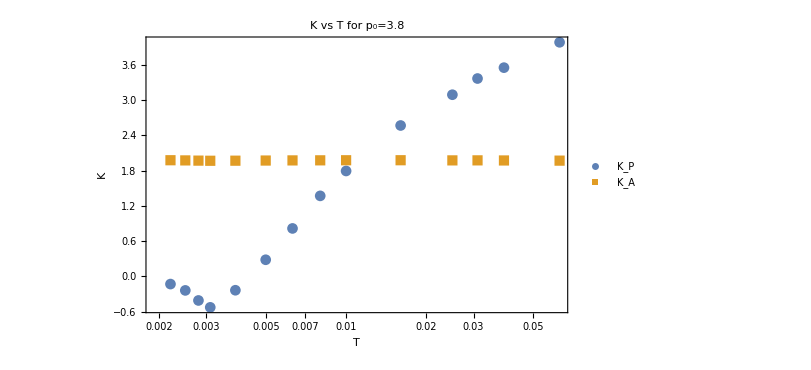
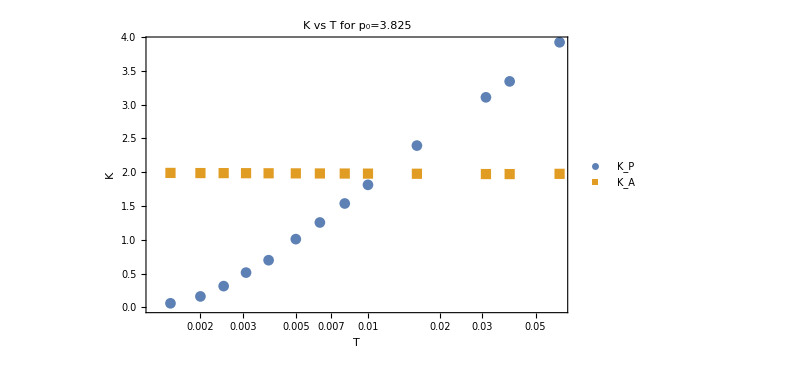
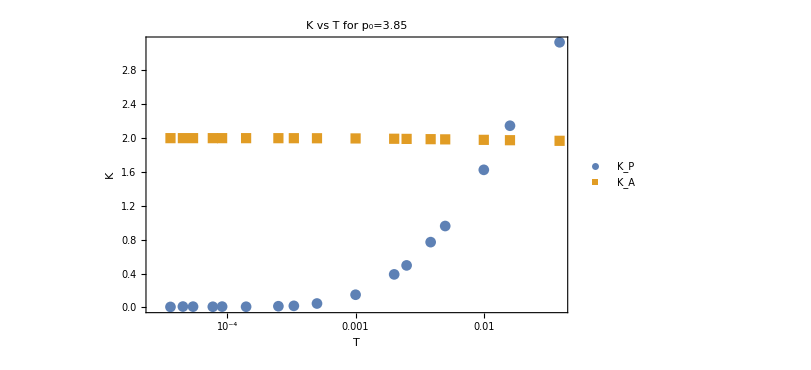

```mathematica
modulusPlotAP=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],bulkModulusArea[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotMarkers->Automatic,PlotLegends->{"K_P","K_A"}]],{p,Length[p0s]}]
```

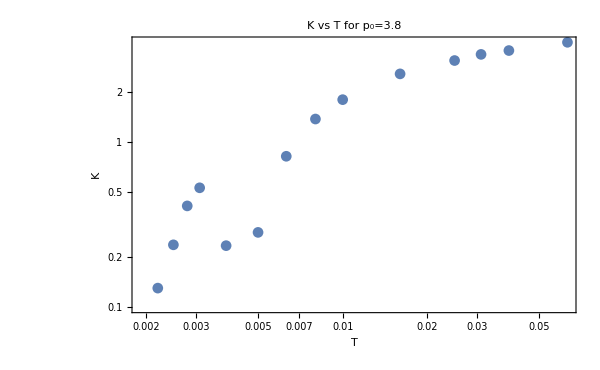
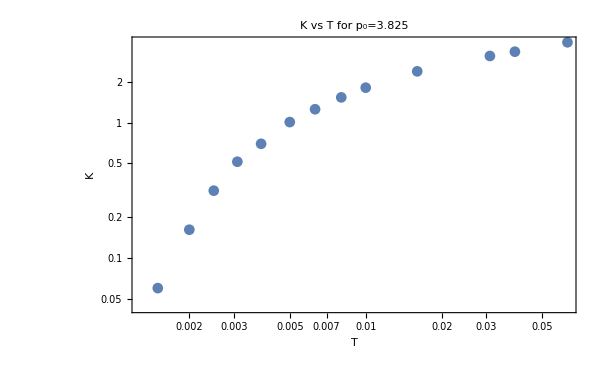
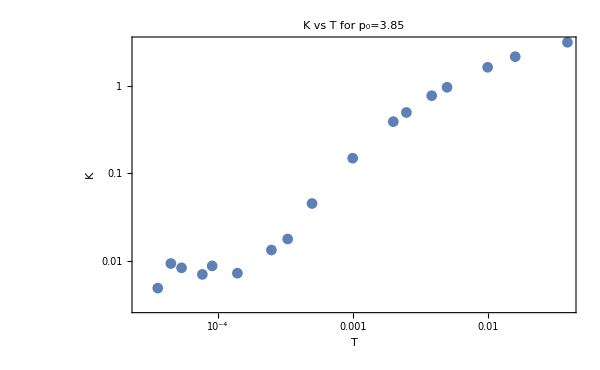

```mathematica
modulusKPPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Abs[bulkModulusPeri[[p,T]]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotMarkers->Automatic]],{p,Length[p0s]}]
```

```mathematica
bulkModulusresults= Grid[Partition[modulusPlot,3]];
bulkModulusresultsAP= Grid[Partition[modulusPlotAP,3]];
```

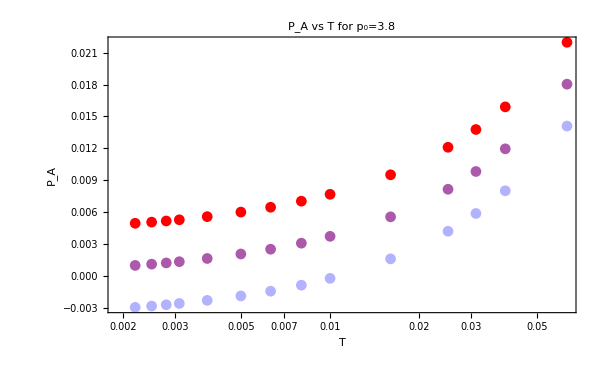
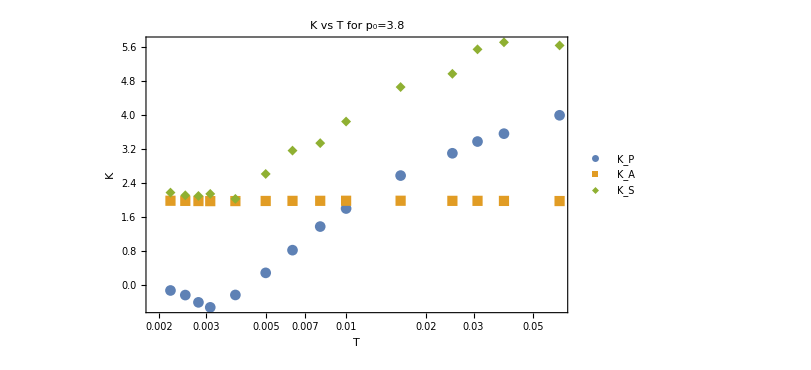
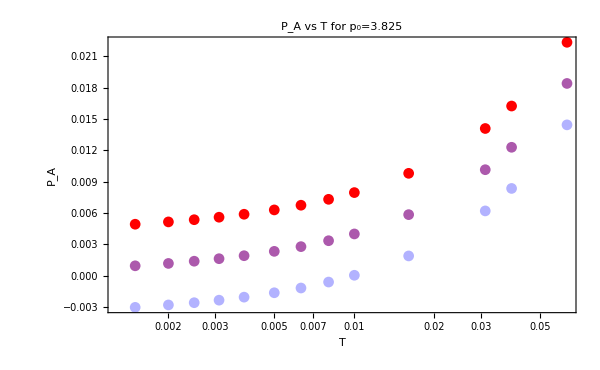
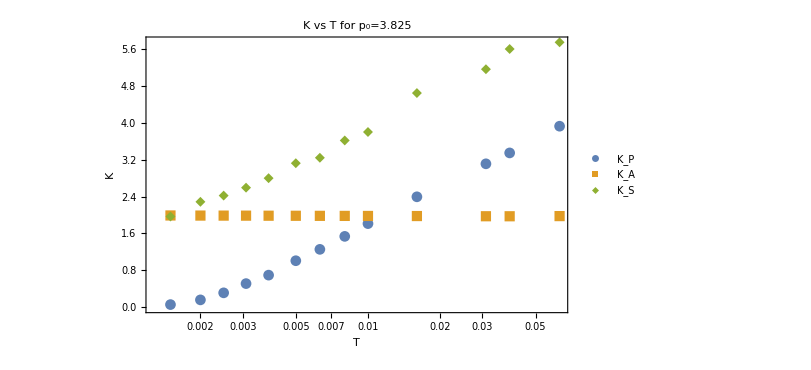
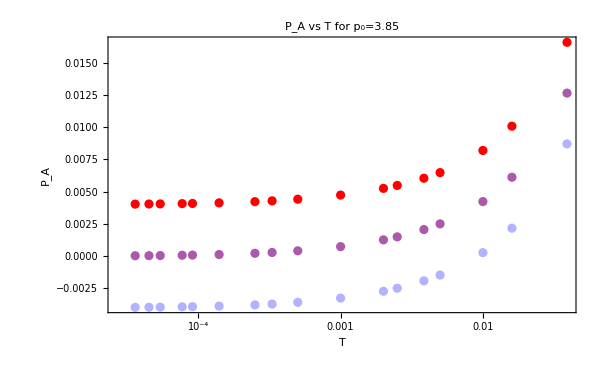
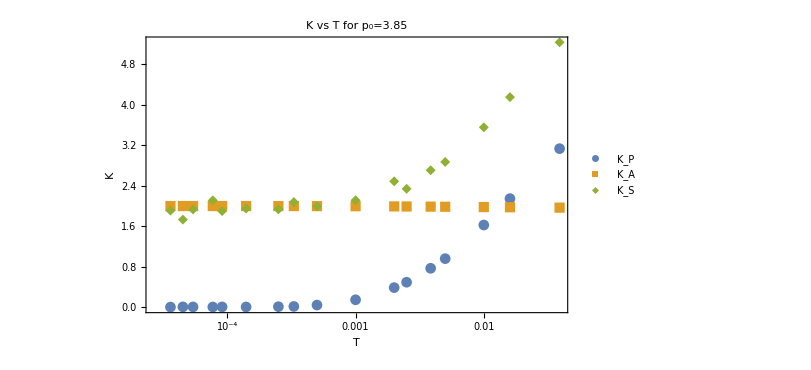
{-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-}

```mathematica
bulkModulusresults=Table[ Grid[Partition[{periPressurePlots[[p]],areaPressurePlots[[p]],modulusPlot[[p]],modulusKPPlots[[p]]},2]],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05232024/bulkModulus"<>ToString[p0s[[p]]]<>".jpeg",bulkModulusresults[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05232024/bulkModulus3.8.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.825.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.85.jpeg}

```mathematica
ClearAll[timePressurePeri]
MemoryInUse[]
MaxMemoryUsed[]
```

320735144

618816056

```mathematica
Table[Export["/home/chengling/Research/updates/05232024/bulkModulus"<>ToString[p0s[[p]]]<>".jpeg",modulusPlot[[p]],ImageResolution->600],{p,3}]
```

{/home/chengling/Research/updates/05232024/bulkModulus3.8.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.825.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/05232024/bulkModulusAP"<>ToString[p0s[[p]]]<>".jpeg",modulusPlotAP[[p]],ImageResolution->600],{p,3}]
```

{/home/chengling/Research/updates/05232024/bulkModulusAP3.8.jpeg,/home/chengling/Research/updates/05232024/bulkModulusAP3.825.jpeg,/home/chengling/Research/updates/05232024/bulkModulusAP3.85.jpeg}